# τ_α from stress autocorrelation

## p_0=3.75

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/SACtime_N4096_p3.7500_T0.01000000_waitingTime39954_idx3.nc","Data"];
```

```mathematica
savefolder375="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/";
```

```mathematica
Tlist={0.063, 0.03105, 0.025 ,0.02, 0.016 ,0.014 ,0.012 ,0.011 ,0.01};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000}

```mathematica
wtlist={10000,10000,10000,10000,10000,10000,10000,13866,39954};
```

```mathematica
sactime375=Table[Import[StringJoin[savefolder375,"SACtime_N4096_p3.7500_T",Tstring[[T]],"_waitingTime",ToString[wtlist[[T]]],"_idx3.nc"],"Data"],{T,Length[Tlist]}];
```

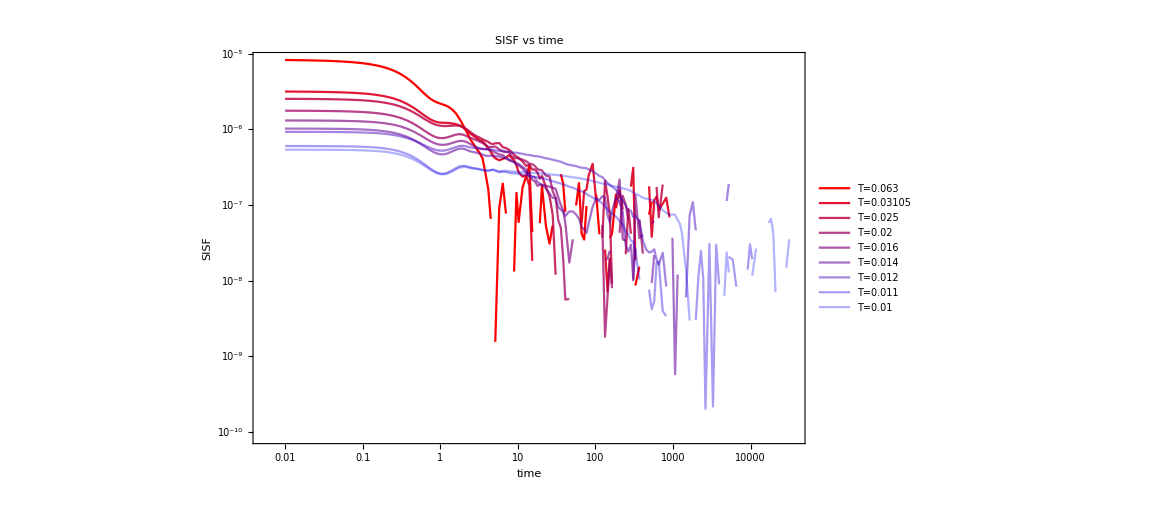

```mathematica
ListLogLogPlot[Table[Table[{sactime375[[T,2,rec]],sactime375[[T,1,rec]]},{rec,Length[sactime375[[T,1]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

## p_0=3.80

```mathematica
savefolder380="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380/";
```

```mathematica
Tlist={0.063, 0.03105, 0.025,0.016, 0.01 ,0.008 ,0.0063 ,0.005 ,0.00385, 0.0031, 0.0028, 0.0025, 0.0022 ,0.002};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000}

```mathematica
wtlist={10000,10000,10000,10000,10000,10000,10000,10000,10000,12440,20650,37314,70000,100000};
```

```mathematica
sactime380=Table[Import[StringJoin[savefolder380,"SACtime_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",ToString[wtlist[[T]]],"_idx3.nc"],"Data"],{T,Length[Tlist]}];
```

```mathematica
ListLogLogPlot[Table[Table[{sactime380[[T,2,rec]],sactime380[[T,1,rec]]},{rec,Min[Length[sactime380[[T,1]]],200]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

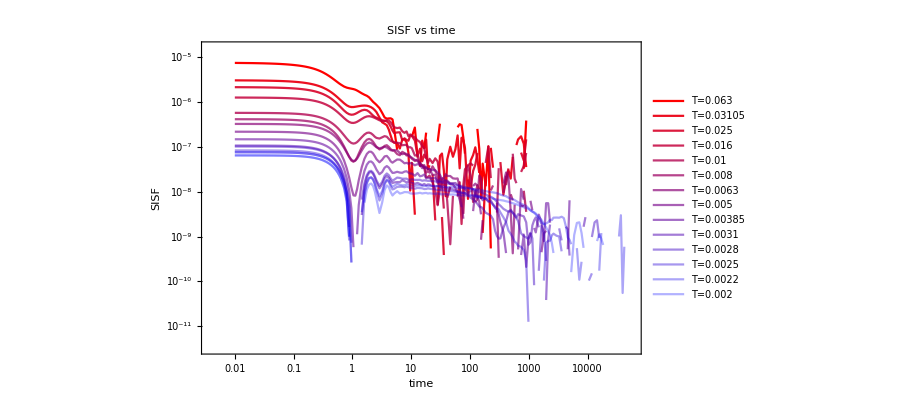

## p_0=3.825

```mathematica
savefolder3825="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p382/";
```

```mathematica
Tlist={0.063 ,0.039,0.025, 0.016 ,0.01 ,0.008, 0.0063, 0.00385 ,0.0025 ,0.002, 0.0018, 0.001 ,0.00067, 0.0005};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00385000,0.00250000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000}

```mathematica
wtlist={10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,10000,12621,39733,100000};
```

```mathematica
sactime3825=Table[Import[StringJoin[savefolder3825,"SACtime_N4096_p3.8250_T",Tstring[[T]],"_waitingTime",ToString[wtlist[[T]]],"_idx3.nc"],"Data"],{T,Length[Tlist]}];
```

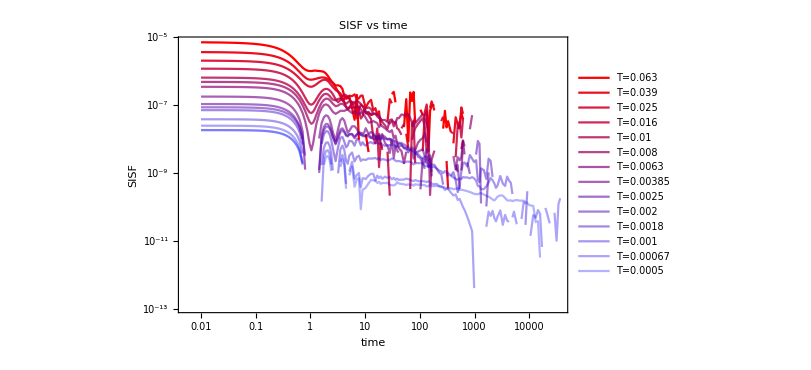

```mathematica
ListLogLogPlot[Table[Table[{sactime3825[[T,2,rec]],sactime3825[[T,1,rec]]},{rec,Min[Length[sactime3825[[T,1]]],200]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```